```mathematica
α[ϵ_]:=(ϵ-1)/(ϵ+1);
```

```mathematica
Limit[α[ϵ],ϵ->Infinity]
Limit[α[ϵ],ϵ->1]
```

1

0

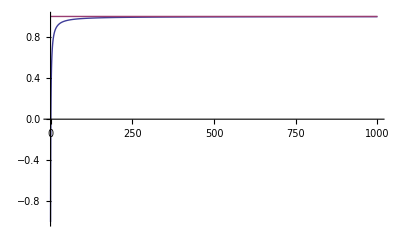

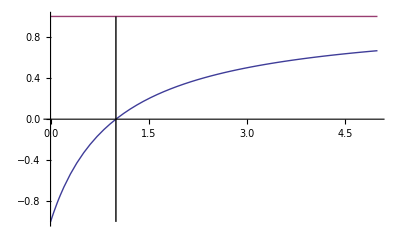

```mathematica
Plot[{α[ϵ],1},{ϵ,0,1000},PlotRange->All]
Show[Plot[{α[ϵ],1},{ϵ,0,5},PlotRange->All],Graphics[Line[{{1,-1},{1,1}}]]]
```

```mathematica
?Line
```

RowBox[{"Line", "[", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["pt", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["pt", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], "]"}] is a graphics primitive which represents a line joining a sequence of points. 
RowBox[{"Line", "[", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["pt", "TI"], StyleBox["11", "TR"]], ",", SubscriptBox[StyleBox["pt", "TI"], StyleBox["12", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["pt", "TI"], StyleBox["21", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], "]"}] represents a collection of lines.

```mathematica
g1=Graphics3D[{Opacity[.2],Cuboid[{0,0,0},{400,400,400}],Opacity[1],Yellow,Sphere[{200,200,200},20],Opacity[1],Black,Text[Style[q,18],{200,200,240}]},Axes->True]
```

-Graphics3D-

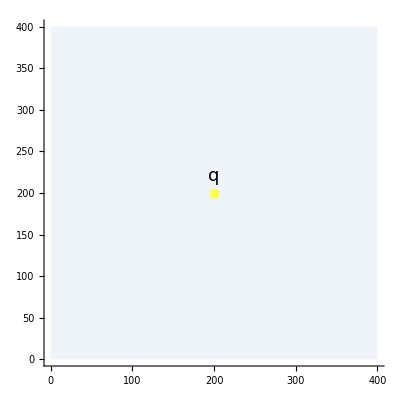

```mathematica
g1b=Graphics[{Opacity[.2],RGBColor[.7,.8,.9],Rectangle[{0,0},{400,400}],Opacity[1],RGBColor[1,1,.3],Disk[{200,200},6],Black,Text[Style[q,18],{200,220}]},Axes->True]
Export["Hq-vacuum2d.pdf",g1b];
```

```mathematica
Export["Hq-vacuum.pdf",g1]
```

Hq-vacuum.pdf

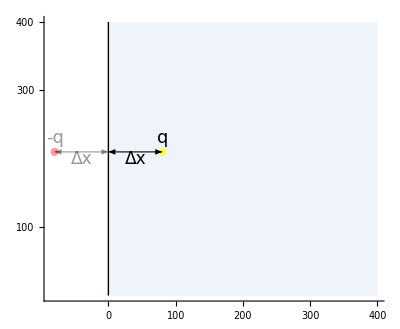

```mathematica
g2=Graphics[{Opacity[.2],RGBColor[.7,.8,.9],Rectangle[{0,0},{400,400}],Opacity[1],RGBColor[1,1,.3],Disk[{80,210},6],Black,Text[Style[q,18],{80,230}],Text[Style[Δx,17],{40,200}],Thick,Line[{{0,0},{0,400}}],Thickness[.002],Arrowheads[{-.02,.02}],Arrow[{{0,210},{80,210}}],(*Image*)Opacity[.4],Red,Disk[{-80,210},6],Black,Text[Style[-q,18],{-80,230}],Text[Style[Δx,17],{-40,200}],Arrow[{{0,210},{-80,210}}]},Axes->True,Ticks->{{0,100,200,300,400},{100,300,400}}]
```

```mathematica
Export["Hq-conduct1.pdf",g2];
```

```mathematica
(*TODO (Expt. 1 and 2): Opacity for image charges etc. to give visual queue that they're not real charges. *)
```

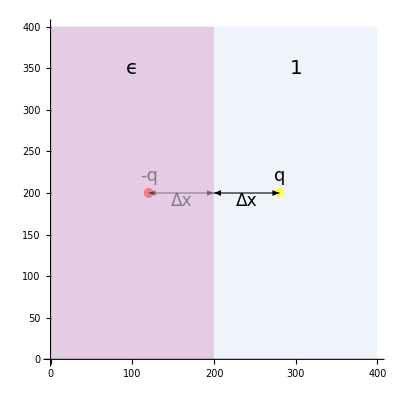

```mathematica
g3=Graphics[{Opacity[.2],RGBColor[.7,.8,.9],Rectangle[{200,0},{400,400}],Purple,Rectangle[{0,0},{200,400}],Opacity[1],Black,Text[Style[ϵ,20],{200-100,350}],Text[Style[1,20],{300,350}],RGBColor[1,1,.3],Disk[{280,200},6],Black,Text[Style[q,18],{280,220}],Text[Style[Δx,17],{240,190}],(*Thick,Line[{{0,0},{0,400}}],*)Thickness[.002],Arrowheads[{-.02,.02}],Arrow[{{200,200},{280,200}}],(*Image*)Opacity[.4],Text[Style[-q,18],{200-80,220}],Red,Disk[{200-80,200},6],Black,Arrow[{{200,200},{200-80,200}}],Text[Style[Δx,17],{200-40,190}]},Axes->True,AxesOrigin->{0,0}]
```

```mathematica
Export["Hq-dielect1.pdf",g3];
```

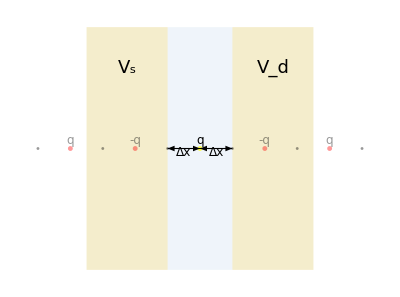

```mathematica
g4=Graphics[{Opacity[.2],RGBColor[.7,.8,.9],Rectangle[{200,0},{360,600}],RGBColor[.8,.65,0],Rectangle[{0,0},{200,600}],Rectangle[{360,0},{560,600}],Opacity[1],Black,Text[Style[Subscript[V, s],18],{200-100,500}],Text[Style[Subscript[V, d],18],{460,500}],RGBColor[1,1,.3],Disk[{280,300},6],Black,Text[Style[q,12],{280,320}],Text[Style[Δx,12],{240,290}],Text[Style[Δx,12],{280+40,290}],(*Thick,Line[{{0,0},{0,400}}],*)Thickness[.002],Arrowheads[{-.02,.02}],Arrow[{{200,300},{280,300}}],Arrow[{{360,300},{280,300}}],(*Image*)Opacity[.4],Text[Style[-q,12],#]&/@{{200-80,320},{200+3*80,320}},Text[Style[q,12],#]&/@{{280-4*80,320},{280+4*80,320}},Red,Disk[#,6]&/@{{120,300},{-40,300},{440,300},{600,300}},
Black,Disk[#,3.5]&/@{{-120,300},{40,300},{200,300},{360,300},{520,300},{680,300}}},Axes->False]
```

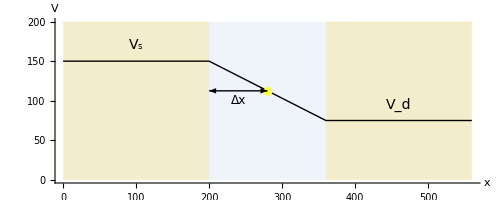

```mathematica
g4b=Graphics[{Opacity[.2],RGBColor[.8,.65,0],Rectangle[{0,0},{200,200}],
Rectangle[{360,0},{560,200}],RGBColor[.7,.8,.9],
Rectangle[{200,0},{360,200}],
Black,Opacity[1],Line[{{0,150},{200,150},{360,75},{560,75}}],
Text[Style[Subscript[V, s],14],{100,170}],Text[Style[Subscript[V, d],14],{460,95}],Text[Style[Δx,12],{240,100}],RGBColor[1,1,.3],Disk[{280,112.5},6],Black,Arrowheads[{-.02,.02}],Arrow[{{200,112.5},{280,112.5}}]},AxesLabel->{x,V},Axes->{True,False}]
```

```mathematica
Export["Hq-conduct2.pdf",g4];
Export["Hq-conduct2b.pdf",g4b];
```

```mathematica
Clear[Subscript[ϵ, vc]]
```

Clear::ssym: ϵ_vc is not a symbol or a string.

```mathematica
(150+75)/2.
```

112.5

```mathematica
Sum[(-1)^k/(2k Δx),{k,1,Infinity}]
```

-Log[2]/(2 Δx)

```mathematica
-Log[2.]
```

-0.693147

```mathematica
Log[E]
```

1

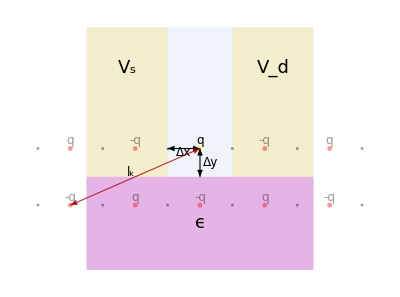

```mathematica
g5=Graphics[{
Opacity[.2],RGBColor[.7,.8,.9],Rectangle[{200,0},{360,600}],RGBColor[.8,.65,0],Rectangle[{0,0},{200,600}],Rectangle[{360,0},{560,600}],Opacity[1],Black,Text[Style[Subscript[V, s],18],{200-100,500}],Text[Style[Subscript[V, d],18],{460,500}],RGBColor[1,1,.3],Disk[{280,300},6],Black,Text[Style[q,12],{280,320}],Text[Style[Δx,12],{240,290}],Text[Style[Δy,12],{280+25,265}],(*Thick,Line[{{0,0},{0,400}}],*)Thickness[.002],Arrowheads[{-.02,.02}],Arrow[{{200,300},{280,300}}],Arrow[{{280,230},{280,300}}],

(*Image*)Opacity[.4],Text[Style[-q,12],#]&/@{{200-80,320},{200+3*80,320}},Text[Style[q,12],#]&/@{{280-4*80,320},{280+4*80,320}},Red,Disk[#,6]&/@{{120,300},{-40,300},{440,300},{600,300}},
Black,Disk[#,3.5]&/@{{-120,300},{40,300},{200,300},{360,300},{520,300},{680,300}},
(* Dielectric *)
Opacity[1],RGBColor[.9,.7,.9],Rectangle[{0,0},{560,230}],Black,Text[Style["ϵ",18],{280,115}],

Opacity[.4],Text[Style[q,12],#]&/@{{200-80,180},{200+3*80,180}},Text[Style[-q,12],#]&/@{{280,180},{280-4*80,180},{280+4*80,180}},

Red,Disk[#,6]&/@{{280,160},{120,160},{-40,160},{440,160},{600,160}},
Black,Disk[#,3.5]&/@{{-120,160},{40,160},{200,160},{360,160},{520,160},{680,160}},

Darker[Red],Opacity[.8],Arrow[{{280,300},{-40,160}}],Black,Opacity[1],
Text[Style[Subscript[l, k],12],{110,240}]


},Axes->False]
```

```mathematica
Export["Hq-fullset.pdf",g5];
```

```mathematica
(280-40)/2
```

120